```mathematica
(* Compute Topple Dynamics *)
(* Written by Yoonyoung Cho, 2/8/2018 *)

(* Coordinate Definition *)
Subscript[e, x]={1,0,0};
Subscript[e, y]={0,1,0};
Subscript[e, h] = {-Sin[θ], Cos[θ],0};
Subscript[e, d]= {Cos[θ], Sin[θ],0};

(* Parametrization *)
(* Note : Currently based on rough estimates *)
p = {
m-> 0.066,
M->0.066/0.005,
l-> 0.35,
Subscript[h, 1] -> 0.22,
Subscript[h, 2] -> 0.47,
Subscript[d, 1]->0.04,
Subscript[d, 2]->0.08,
g-> 9.81
};

(* Frame Positions *)
Subscript[r, p]=-Subscript[d, 1] Subscript[e, x];
Subscript[r, M]= Subscript[r, p]+Subscript[d, 1]/2 Cos[θ] Subscript[e, d]+Subscript[h, 1] Subscript[e, h];
Subscript[r, m]= Subscript[r, m]+Subscript[h, 2] Subscript[e, h]-Subscript[d, 2] Subscript[e, d]-l Subscript[e, y];
```

```mathematica
(* Torque Calculation *)
Subscript[τ, m] = (Subscript[r, m]-Subscript[r, p])×(-m g Subscript[e, y]);
Subscript[τ, M]=(Subscript[r, M]-Subscript[r, p])×(-M g Subscript[e, y]);
tau = Simplify[Dot[(Subscript[τ, m]+Subscript[τ, M]),{0,0,1}]]
TraditionalForm[tau]
```

1/2 g ((-M Cos[θ]^2+m (-2+Sin[θ]^2)) d_1+2 (7 m Cos[θ] d_2+Sin[θ] ((m+M) h_1+7 m h_2)))

1/2 g (2 (7 d_2 m cos(θ)+sin(θ) (h_1 (m+M)+7 h_2 m))+d_1 (m (sin^2(θ)-2)-M cos^2(θ)))

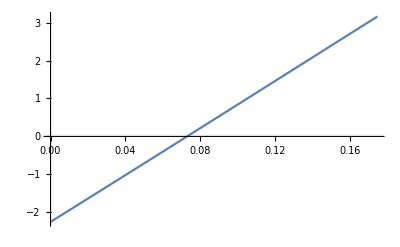

4.17656

```mathematica
Plot[tau/.p, {θ, 0, 10°}]
(180/π θ)/.FindRoot[tau/.p, {θ,0,10°}]
```